## Histogram Equalization II

### Problem #1

Read in Vermeer’s L30. Observe that there are not many different values: the histogram

Accordingly, when doing histogram equalization, there are a large number of "empty" spaces in the equalized version, as you can see from the bottom histogram plot above. Your goal in this project is to create a modified histogram equalization method that "fills in" these empty spaces in the histogram. You may wish to begin with the following code, which shows the myHistEQ[ ] function, ready for your modifications.

```mathematica
img = Import[NotebookDirectory[]<>"VermeerL30.tiff"]
```

-Graphics-

### (a) Plot the ImageHistogram of L30

Observe that almost all the values are pretty small... this is why it is so dark. Does ImageAdjust help? Why not?

```mathematica
ImageCollage[{ImageHistogram[img],ImageHistogram[ImageAdjust[img]]}]
```

-Graphics-

ImageAdjust does not help at all since ImageAdjust expand the max and min of origin image to 1 and 0.

### (b) Plot the ImageHistogram of the HistogramTransform

Observe that the number of nonzero values is small: each of the three colors has big gaps in the histogram where there are no values.

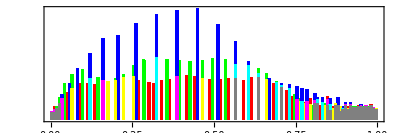

```mathematica
ImageHistogram[HistogramTransform[img]]
```

### (c) Develop an algorithm to “fill in the holes” in the histogram.

Your method should take in an image (like the histogram transformed L30) that has lots of holes in the histogram. The output should be an image that does not have lots of holes in its histogram.

You may wish to operate first with a simpler grayscale image. In case you want to “get inside” the HistogramTransform process, here is a version that works only on one channel at a time.

```mathematica
myHistEQ[iMat_]:=Module[{},
pixels=Round[255 Flatten[iMat]];
{h,w}=Dimensions[iMat];
hPDF=BinCounts[pixels,{0,256,1}]/(h*w);
hCDF=Accumulate[hPDF];
outPix=255 hCDF[[pixels+1]];
Partition[outPix,w]];
```

To call this routine:

myHistEQ[ImageData[bwImage]]

where bwImage is a single channel image like a grayscale or like the R channel of an RGB image.

```mathematica
histeq = myHistEQ[ImageData[ColorConvert[img,"Grayscale"]]];
newimgGray = ImageCompose[Image[histeq], ColorConvert[img, "Grayscale"]];
ImageCollage[{ImageHistogram[HistogramTransform[ColorConvert[img, "Grayscale"]]],ImageHistogram[HistogramTransform[newimgGray]]}]
ImageCollage[{ImageHistogram[ColorConvert[img, "Grayscale"]],ImageHistogram[newimgGray]}]
```

-Graphics-

-Graphics-

```mathematica
newImgRGB = ColorCombine[{ImageCompose[Image[myHistEQ[ImageData[ColorSeparate[img, "R"]]]],ColorSeparate[img,"R"]],ImageCompose[Image[myHistEQ[ImageData[ColorSeparate[img, "G"]]]],ColorSeparate[img,"G"]],ImageCompose[Image[myHistEQ[ImageData[ColorSeparate[img, "B"]]]],ColorSeparate[img,"B"]]},"RGB"];
newImgHSB = ColorCombine[{ImageCompose[Image[myHistEQ[ImageData[ColorSeparate[img, "H"]]]],ColorSeparate[img,"H"]],ImageCompose[Image[myHistEQ[ImageData[ColorSeparate[img, "S"]]]],ColorSeparate[img,"S"]],ImageCompose[Image[myHistEQ[ImageData[ColorSeparate[img, "V"]]]],ColorSeparate[img,"V"]]},"HSB"];
ImageCollage[{newImgRGB,newImgHSB}]
```

-Graphics-

```mathematica
ImageCollage[{ImageHistogram[HistogramTransform[img]],ImageHistogram[HistogramTransform[newImgRGB]],ImageHistogram[HistogramTransform[newImgHSB]]}]
```

HistogramTransform::cscycl: HistogramTransform does not support images with a cyclic Hue channel. Assuming Automatic color space instead.

-Graphics-